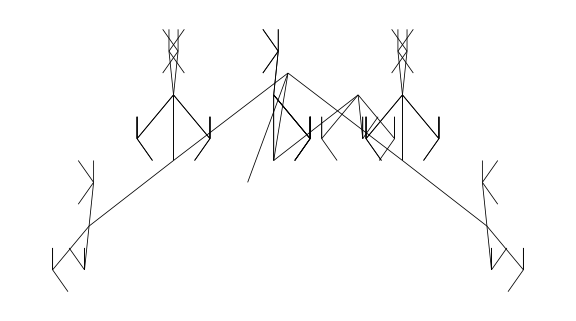

```mathematica
(*Remains to be done: writing a loop of around 1000 to iterate over the seeds and save each case as tree#SEED in a directory
seed1=Input[]*)
fractalTree[pt:{_,_},θorient_: π/2,θsep_: π/9,depth_Integer: 9]:=Module[{pt2},If[depth==0,Return[]];
pt2=pt+{2Cos[depth]Sin[θorient]^3,Normalize[Re[Tan[θorient+0.01]]]}*depth;DeleteCases[Flatten@{Line[{pt,pt2},VertexColors->{Gray,Black}],fractalTree[pt2,3(θorient-(1.5*θsep)),θsep,depth-1],fractalTree[pt2,(θorient+(0.5*θsep)),θsep,depth-1],fractalTree[pt2,(θorient+(1.5*θsep)),θsep,depth-1]},Null]];
seed1 = 4;
SeedRandom[seed1]
Graphics[{Thickness[.001], fractalTree[{0,0},π/3,π/3,5]}, ImageSize->Large]

For[seed1 = 35, seed1 < 35,seed1++,img = Graphics[{Thickness[.001], fractalTree[{0,0},π/3,π/3,10]}, ImageSize->{3280}]; Export[FileNameJoin[{"/TREES/TRT-L8-0/",StringJoin["Ttree-L-8-0[",ToString[seed1],"].png"]}],img, "PNG"]]
```

```mathematica
3
```

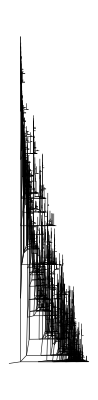

```mathematica
Show[%1726,ImageSize->Full]
```

```mathematica
-**
```

```mathematica
6
```

6

```mathematica
0
```

```mathematica
Show[%20,ImageSize->{360,3},AspectRatio->Full]
```

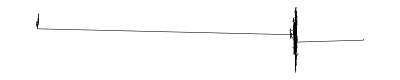

```mathematica
Show[%189,ImageSize->Full]
```

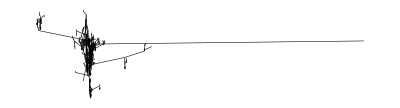

```mathematica
Show[%172,ImageSize->Full]
```

```mathematica
4
```

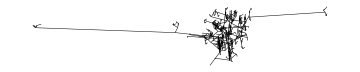

```mathematica
Show[%98,ImageSize->Medium]
```

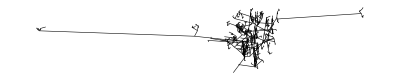

```mathematica
Show[%99,ImageSize->Full]
```

```mathematica
.
```

```mathematica
RealDigits
```

-Graphics-

/tmp/tree2.png

```mathematica
Show[%432, ImageSize->Full]
```

```mathematica
m
```

```mathematica
MapThread[Print,{{"a","b","c"},{"A","B","C"},{1,2,3}}];
```

aA1

bB2

cC3

```mathematica
(*


fractalTree[pt:{_,_},θorient_: π/2,θsep_: π/9,depth_Integer: 9]:=Module[{pt2},If[depth==0,Return[]];
pt2=pt+{Re[Log10[θorient]]*Cos[θorient],Normalize[θorient]*Sin[θorient]}*depth;DeleteCases[Flatten@{Line[{pt,pt2},VertexColors->{Gray, Black}],fractalTree[pt2,RandomReal[{1.1,8.9}](θorient-θsep),θsep,depth-1],fractalTree[pt2,Cos[depth^3]*Sin[depth]*(θorient+θsep),θsep,depth-1]},Null]];

fractalTree[pt:{_,_,_},θorient_: π/2,θsep_: π/9,θsep2_: π/9,depth_Integer: 9]:=Module[{pt2},If[depth==0,Return[]];
pt2=pt+{Cos[θorient],Sin[θorient]}*depth;

ptDeleteCases[Flatten@{Line[{pt,pt2},VertexColors->{RGBColor[Sin[depth],Cos[depth] , Sqrt[depth]],RandomColor[4]}],fractalTree[pt2,1.6*(θorient-θsep),θsep,depth-1],fractalTree[pt2,1.3*(θorient+θsep),θsep,depth-1]},Null]];
Graphics[{Thickness[.002], fractalTree[{0,0},π/2,π/8,10]}]*)
```

```mathematica
m1=DiscreteMarkovProcess[{1,0,0},{{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}}]
```

DiscreteMarkovProcess[{1,0,0},{{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}}]

```mathematica
GraphPlot[m1,SelfLoopStyle->True,MultiedgeStyle->True]
```

GraphPlot::grph: m1 is not a valid graph.

```mathematica
GraphPlot[{{1,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}},SelfLoopStyle->True,MultiedgeStyle->True]
```

```mathematica
(**)
```